Our problem here is to compute for absolute error which is the difference between the actual value and the approximate value given by the Taylor’s polynomial.

Approximate the function y=x^(1/5)  by a Taylor’s polynomial of degree 3.

Approximate the function f(x)=x^(1/5) by a Taylor polynomial of degree 3 at a =5.

SOLUTION

```mathematica
f=x^(1/5)(* Given function *)
f'=D[f,x](* First derivative *)
f''=D[f,{x,2}](* Second derivative *)
f'''[x_]=D[f,{x,3}](* Third derivative *)
(f^iv)[x_]=D[f,{x,4}](* Fourth derivative *)
```

x^(1/5)

```mathematica
(* Given function: x^(1/5)*)
```

First derivative: 1/(5 x^(4/5))

-4/(25 x^(9/5))

Second derivative: -4/(25 x^(9/5))

3rd derivative: 36/(125 x^(14/5))

4th derivative: -504/(625 x^(19/5))

36/(125 x^(14/5))

Set::write: Tag Power in x^(iv/5)[x_] is Protected.

-504/(625 x^(19/5))

```mathematica
x^(1/5)(* given function. *)
```

1/(5 x^(4/5))

-4/(25 x^(9/5))

36/(125 x^(14/5))

Set::write: Tag Power in x^(iv/5)[x_] is Protected.

-504/(625 x^(19/5))

At x=5

f=5^(1/5)

f'=1/(5(5)^(4/5))

f''=-4/(25(5^(9/5)))

f'''=36/(125(5^(14/5)))

f^iv =-504/(4!*625 (5)^(19/5))

The Taylor’s series is -Graphics-. By substitution we have the approximation for degree 3:

f(x)=T_3(x)=x^(1/5)=5^(1/5)+1/(5(5)^(4/5))(x−5)−4/((2)25(5^(4/5)))(x−a)^2+36/((6)125(5^(14/5)))(x−3)^3

```mathematica
Series[x^(1/5),{x,5,4}](* The output below verifies the answer. *)
```

5^(1/5)+(x-5)/(5 5^(4/5))-(2 (x-5)^2)/(125 5^(4/5))+(6 (x-5)^3)/(3125 5^(4/5))-(21 (x-5)^4)/(78125 5^(4/5))+O[x-5]^5

============================================================================================

What is the absolute error when x=4 for degree 3.

SOLUTION: Error = |Exact value - approximate value|

=|x^(1/5)-(5^(1/5)+(x-5)/(5 5^(4/5))-(2 (x-5)^2)/(125 5^(4/5))+(6 (x-5)^3)/(3125 5^(4/5)))|

```mathematica
h[x_]:=Abs[x^(1/5)-(5^(1/5)+(x-5)/(5 5^(4/5))-(2 (x-5)^2)/(125 5^(4/5))+(6 (x-5)^3)/(3125 5^(4/5)))];(* Absolute error at x=4 *)
h[4]//N
```

0.0000876131

```mathematica
Plot[{x^(1/5),5^(1/5)+(x-5)/(5 5^(4/5))-(2 (x-5)^2)/(125 5^(4/5))+(6 (x-5)^3)/(3125 5^(4/5))},{x,0,10},GridLines->{{5},{0}},GridLinesStyle->Directive[Red, Dashed],PlotLabels->{"Given function x^(1/5)","Taylor's Approximation"},ImageSize->{500}]
```

-Graphics-

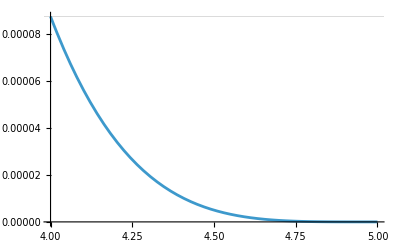

```mathematica
Plot[Abs[x^(1/5)-(5^(1/5)+(x-5)/(5 5^(4/5))-(2 (x-5)^2)/(125 5^(4/5))+(6 (x-5)^3)/(3125 5^(4/5)))],{x,4,5},GridLines->{{0},{0.00008761312319505166},GridLinesStyle->Directive[Red, Thick]}]
```

```mathematica
h[5](* Absolute error is at x=5 *)
```

0